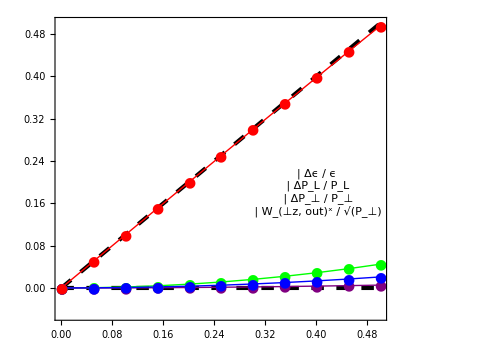

```mathematica
(*ANISOTROPIC HADRON RESONANCE GAS*)

(* Π = -0.5 Subscript[P, eq]*)

T0 = 0.155;
αT = 0.5830;
αL = 0.5830;
Λ = 0.1974; (* GeV *)
frac=Table[0.05*i,{i,0,10}];

(*I should plot the PL and PT matching conditions*)
(*As well as the pi_perp_xx*)

Δϵoverϵdata = {0.0,5.417*10^-05,0.0002167,0.0004875,0.0008667,0.001354,0.00195,0.002654,0.003466,0.004387,0.005415};

ΔPLoverPLdata = {0.0,0.0004489,0.001795,0.00404,0.007182,0.01122,0.01616,0.022,0.02874,0.03638,0.04491};

ΔPToverPTdata ={0.0,0.0002084,0.0008335,0.001875,0.003334,0.005209,0.007501,0.01021,0.01334,0.01688,0.02084};

Wxzdata = {0.0,0.05,0.09996,0.1499,0.1997,0.2494,0.299,0.3484,0.3975,0.4465,0.4952};

style={Directive[RGBColor[0,0,0],AbsoluteThickness[3],Dashing[Medium]],Directive[RGBColor[0,0,0],AbsoluteThickness[3],Dashing[Medium]]};

legend1=Panel[Grid[{{Graphics[{Purple,Disk[]},ImageSize->10],Style["Δϵ / ϵ",FontSize->16]},

{Graphics[{Green,Disk[]},ImageSize->10],Style["ΔP_L / P_L",FontSize->16]},{Graphics[{Blue,Disk[]},ImageSize->10],Style["ΔP_⊥ / P_⊥",FontSize->16]},
{Graphics[{Red,Disk[]},ImageSize->10],Style["W_(⊥z, out)^x / √(P_⊥)",FontSize->16]}}],Background->White];

Δϵoverϵplot = Table[{frac[[i]],Δϵoverϵdata[[i]]},{i,1,Length[frac]}];
ΔPToverPTplot = Table[{frac[[i]],ΔPToverPTdata[[i]]},{i,1,Length[frac]}];
ΔPLoverPLplot  = Table[{frac[[i]],ΔPLoverPLdata [[i]]},{i,1,Length[frac]}];
Wxzplot = Table[{frac[[i]],Wxzdata[[i]]},{i,1,Length[frac]}];

Show[{{
Plot[{x,0.0},{x,0,0.5},PlotRange->{-0.-0.05,0.5},ImageSize->{500,400},PlotStyle->style,Frame->True,Axes->False,BaseStyle->{FontSize->18},AspectRatio->0.7],
ListPlot[{ΔPLoverPLplot,Δϵoverϵplot,ΔPToverPTplot,Wxzplot},Joined->{True},PlotRange->{-0.1,0.5},ImageSize->600,Frame->True,Axes->False,PlotMarkers->{{●,14},{●,14},{●,14},{●,14}},PlotStyle->{{Green,Thick},{Purple,Thick},{Blue,Thick},{Red,Thick}},BaseStyle->{FontSize->18},AspectRatio->0.7]}
},Epilog->{Inset[legend1,{0.4,0.18}]},ImageSize->{500,400},FrameLabel->{"W_(⊥z, in)^x / √(P_⊥)"}]
```